```mathematica
(*1*)
```

```mathematica
Clear["Global`*"]
BasisFunc[n_]:=Function[{x},Sqrt[(2n+1)/2]LegendreP[n,x]]
BasisMax=10;

qFunc[x_]=PDF[NormalDistribution[0.1,0.2],x];
```

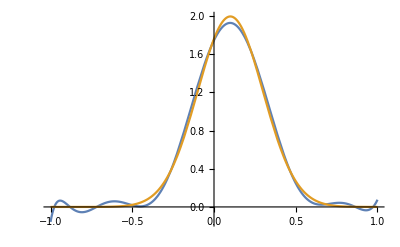

(0 | √3 | 0 | √7 | 0 | √11 | 0 | √15 | 0 | √19 | 0
0 | 0 | √15 | 0 | 3 √3 | 0 | √39 | 0 | √51 | 0 | 3 √7
0 | 0 | 0 | √35 | 0 | √55 | 0 | 5 √3 | 0 | √95 | 0
0 | 0 | 0 | 0 | 3 √7 | 0 | √91 | 0 | √119 | 0 | 7 √3
0 | 0 | 0 | 0 | 0 | 3 √11 | 0 | 3 √15 | 0 | 3 √19 | 0
0 | 0 | 0 | 0 | 0 | 0 | √143 | 0 | √187 | 0 | √231
0 | 0 | 0 | 0 | 0 | 0 | 0 | √195 | 0 | √247 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √255 | 0 | 3 √35
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √323 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √399
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

{-4.12546,16.1873,-4.09697,25.3596,-20.9989,15.8573,0.869546,29.1889,-16.8327,0.,0.}

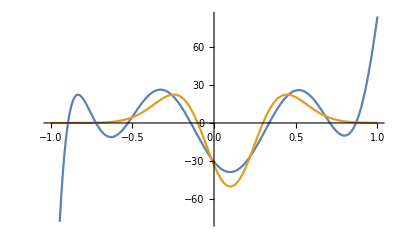

```mathematica
q=Table[NIntegrate[qFunc[x]BasisFunc[n][x],{x,-1,1}],{n,0,BasisMax}];
Plot[{q.Table[BasisFunc[n][x],{n,0,BasisMax}],qFunc[x]},{x,-1,1},PlotRange->All]


(LegDerivative={ConstantArray[0,BasisMax+1]}~Join~Table[Normal[SparseArray[Band[l,1,-2]->Array[(2(l-2#)-1)&,Quotient [l,2]+1,0],{BasisMax+1}]],{l,1,BasisMax}])//MatrixForm;
(LegDerivative=Transpose[MapIndexed[#1Sqrt[(2#2[[1]]-1)/(2#2[[2]]-1)]&,LegDerivative,{2}]])//MatrixForm

MatrixPower[LegDerivative,2].q
Plot[{%.Table[BasisFunc[n][x],{n,0,BasisMax}],Evaluate[D[qFunc[x],{x,2}]]},{x,-1,1}]
```

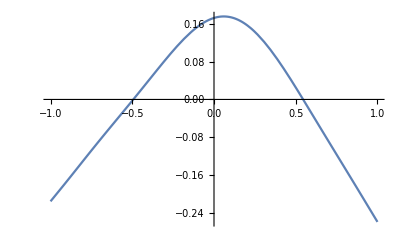

{0.406582,0.0585809}

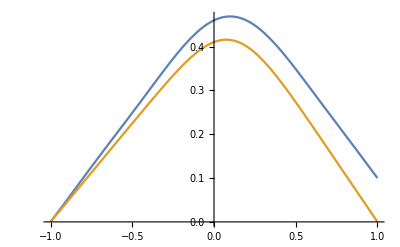

```mathematica
T=-Inverse[MatrixPower[LegDerivative,2][[;;-3,3;;]]].(q[[;;-3]]);
Plot[{T.Table[BasisFunc[n][x],{n,2,BasisMax}]},{x,-1,1},PlotRange->All]

(*Пусть граничные условия y[-1]=a, y'[-1]=b*)
a=0;
b=-0.5;

m=({{BasisFunc[0][-1], BasisFunc[1][-1]}, {0, D[BasisFunc[1][x],x]/.x->1}});
stpodg={a-T.Table[BasisFunc[n][-1],{n,2,BasisMax}],b-D[T.Table[BasisFunc[n][x],{n,2,BasisMax}],x]/.x->1};
solgr=LinearSolve[m,stpodg]

T=solgr~Join~T;

sol=y/.NDSolve[{y''[x]==-qFunc[x],y[-1]==0,y[1]==0},y,x][[1]];
Plot[{T.Table[BasisFunc[n][x],{n,0,BasisMax}],sol[x]},{x,-1,1},PlotRange->All]
```

```mathematica
(*2*)
```

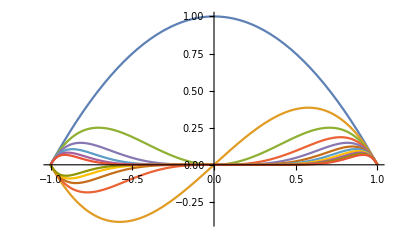

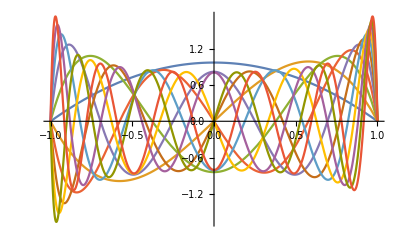

```mathematica
Clear["Global`*"]
BasisFunc[n_] =  #^n(1-#^2)&;
BasisMax = 10;
qFunc[x_]=PDF[NormalDistribution[0.1,0.2],x];
Basis := Table[BasisFunc[n][#], {n,0,BasisMax}] &;
Plot[Evaluate[Basis[x]],{x,-1,1}, PlotRange -> All]
ONBBasis=Orthogonalize[Basis[x],Integrate[#1*#2,{x,-1,1}]&];
Plot[Evaluate[ONBBasis],{x,-1,1}, PlotRange -> All]
```

```mathematica
(*не в ОНБ*)
GramMatrix = Chop[Table[NIntegrate[BasisFunc[n][x] * BasisFunc[m][x],{x,-1,1}],{n,0,BasisMax},{m,0,BasisMax}]];

q = LinearSolve[GramMatrix,Table[NIntegrate[BasisFunc[n][x] * qFunc[x], {x,-1,1}], {n, 0, BasisMax}]];
L =Chop @ Transpose @ Table[LinearSolve[GramMatrix,Table[NIntegrate[D[BasisFunc[i][x],{x,2}] * BasisFunc[n][x],{x,-1,1}, AccuracyGoal->15],{n,0,BasisMax}]],{i,0,BasisMax}];
(*оператор второй производной отрицательно определен, поэтому чтобы применить формулу для функционала (Lphi,phi)-2(phi,f) будем рассматривать уравенние -Δphi=rho (оператор -Δ положительно определен)*)
L=-L;
phi=Table[Subscript[c,i],{i,0,BasisMax}];
func=(L.phi).GramMatrix.phi-2*(phi.GramMatrix.q);
```

{c_0→0.410392,c_1→0.137884,c_2→-0.465109,c_3→-0.486114,c_4→0.836046,c_5→0.994087,c_6→-1.10548,c_7→-1.01095,c_8→0.840585,c_9→0.393846,c_10→-0.267472}

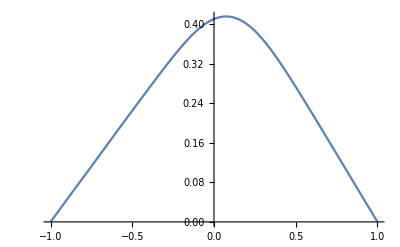

```mathematica
reg=Cuboid[Table[-20,BasisMax+1],Table[20,BasisMax+1]];
sol=NMinimize[func,phi∈reg][[2]]
Plot[Basis[x].phi/.sol,{x,-1,1}]
```

```mathematica
(*в ОНБ*)
```

```mathematica
q=Table[NIntegrate[ONBBasis[[n+1]] * qFunc[x], {x,-1,1}], {n, 0, BasisMax}];
L=-Chop@Table[NIntegrate[D[ONBBasis[[n+1]],{x,2}] *ONBBasis[[m+1]],{x,-1,1}, AccuracyGoal->BasisMax],{m,0,BasisMax},{n,0,BasisMax}];
phi=Table[Subscript[c,i],{i,0,BasisMax}];
func=(L.phi).phi-2*(phi.q);
reg=Cuboid[Table[-20,BasisMax+1],Table[20,BasisMax+1]];
sol=NMinimize[func,phi∈reg][[2]]
Plot[ONBBasis.phi/.sol,{x,-1,1}]
```

{c_0→0.379819,c_1→0.0246965,c_2→-0.0386787,c_3→-0.0091091,c_4→0.00923905,c_5→0.00367637,c_6→-0.00250008,c_7→-0.00141802,c_8→0.000657191,c_9→0.000401539,c_10→-0.000134542}

-Graphics-

```mathematica
(*Нейнман y'[-1]=a, y'[-1]=b, будем решать в ОНБ*)
```

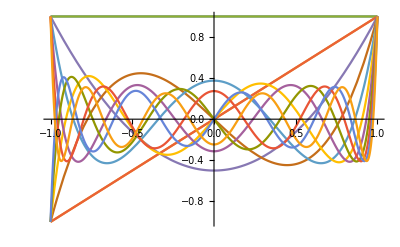

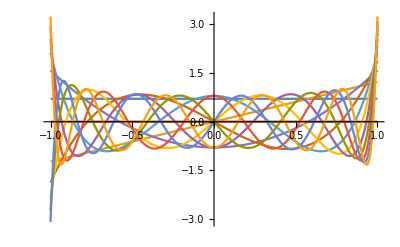

```mathematica
BasisMax =10;
Basis :={1,#}~ Join~Table[BasisFunc[n][#], {n,0,BasisMax}] &;
Plot[Evaluate[Basis[x]],{x,-1,1}, PlotRange -> All]
ONBBasis=Orthogonalize[Basis[x],Integrate[#1*#2,{x,-1,1}]&];
Plot[Evaluate[ONBBasis],{x,-1,1}, PlotRange -> All]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{13}

{c_0→-0.0693546,c_1→-0.349665,c_2→-0.269464,c_3→-0.104592,c_4→-0.179321,c_5→-0.0179623,c_6→0.0286075,c_7→0.0076402,c_8→-0.00764139,c_9→-0.00323199,c_10→0.00216415,c_11→0.000904414,c_12→-0.000457419}

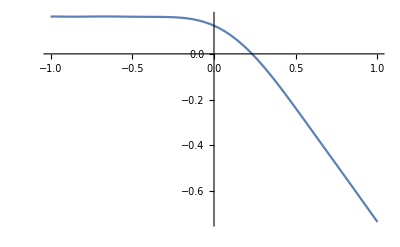

```mathematica
a=0;
b= a - Integrate[qFunc[x],{x,-1,1}];;
q=Table[NIntegrate[ONBBasis[[n+1]] * qFunc[x], {x,-1,1}], {n, 0, BasisMax+2}];
grad=Chop@Table[NIntegrate[D[ONBBasis[[n+1]],{x,1}] *ONBBasis[[m+1]],{x,-1,1}, AccuracyGoal->BasisMax],{m,0,BasisMax+1},{n,0,BasisMax+2}];
phi=Table[Subscript[c,i],{i,0,BasisMax+2}];
Dimensions[phi]
func=1/2*(grad.phi).(grad.phi)-(phi.q)+a*(ONBBasis.phi/.x->-1)-b*(ONBBasis.phi/.x->1);

reg=Cuboid[Table[-100,BasisMax+3],Table[100,BasisMax+3]];
sol=NMinimize[func,phi∈reg][[2]]
Plot[ONBBasis.phi/.sol,{x,-1,1}]
```

```mathematica
(*Дирихле y[-1]=a, y[-1]=b, будем решать в ОНБ*)
```

-Graphics-

-Graphics-

{c_0→0.379819,c_1→0.0246965,c_2→-0.0386787,c_3→-0.0091091,c_4→0.00923905,c_5→0.00367637,c_6→-0.00250008,c_7→-0.00141802,c_8→0.000657191,c_9→0.000401539,c_10→-0.000134542}

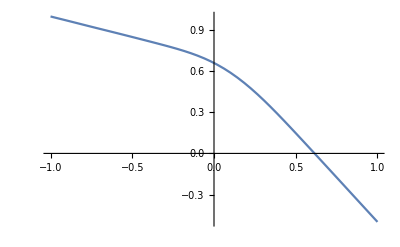

```mathematica
BasisMax = 10;
a=1;
b=-0.5;

podg=(b-a)/2*x+(a+b)/2;

Basis :=Table[BasisFunc[n][#], {n,0,BasisMax}] &;
Plot[Evaluate[Basis[x]],{x,-1,1}, PlotRange -> All]
ONBBasis=Orthogonalize[Basis[x],Integrate[#1*#2,{x,-1,1}]&];
Plot[Evaluate[ONBBasis],{x,-1,1}, PlotRange -> All]

q=Table[NIntegrate[ONBBasis[[n+1]] * qFunc[x], {x,-1,1}], {n, 0, BasisMax}];
L=-Chop@Table[NIntegrate[D[ONBBasis[[n+1]],{x,2}] *ONBBasis[[m+1]],{x,-1,1}, AccuracyGoal->BasisMax],{m,0,BasisMax},{n,0,BasisMax}];
phi=Table[Subscript[c,i],{i,0,BasisMax}];
func=(L.phi).phi-2*(phi.q);
reg=Cuboid[Table[-20,BasisMax+1],Table[20,BasisMax+1]];
sol=NMinimize[func,phi∈reg][[2]]
Plot[(ONBBasis.phi/.sol)+podg,{x,-1,1}]
```